```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/edric/Documents/Masters/FreeQSW/examples/Application 2

```mathematica
G = Import["graphs/1_G1.graphml"]
```

$Failed

```mathematica
Export["harary.graphml",HararyGraph[4,8]]
```

harary.graphml

```mathematica
A1={{1,2,3,4},{0},{0},{0},{0}} + 1
```

{{2,3,4,5},{1},{1},{1},{1}}

```mathematica
AdjacencyGraph[A1]
```

AdjacencyGraph::matsq: Argument {{2,3,4,5},{1},{1},{1},{1}} at position 1 is not a non-empty square matrix.

AdjacencyGraph[{{2,3,4,5},{1},{1},{1},{1}}]

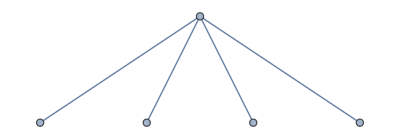

```mathematica
edges=Union[Sort/@Flatten[MapIndexed[Thread[First[#2]<->#]&,A1]]];
g=Graph[Range[Length[A1]],edges]
```

```mathematica
A2={{1,2,3,4},{0,5,6},{0,7,8},{0,9,10},{0,11,12},{1},{1},{2},{2},{3},{3},{4},{4}} + 1
```

{{2,3,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{2},{2},{3},{3},{4},{4},{5},{5}}

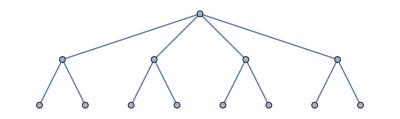

```mathematica
edges=Union[Sort/@Flatten[MapIndexed[Thread[First[#2]<->#]&,A2]]];
g=Graph[Range[Length[A2]],edges]
```

```mathematica
A3={{1,2,3,4},{0,5,6},{0,7,8},{0,9,10},{0,11,12},{1,13,14},{1,15,16},{2,17,18},{2,19,20},{3,21,22},{3,23,24},{4,25,26},{4,27,28},{5},{5},{6},{6},{7},{7},{8},{8},{9},{9},{10},{10},{11},{11},{12},{12}}+1
```

```mathematica
{{2,3,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{2,14,15},{2,16,17},{3,18,19},{3,20,21},{4,22,23},{4,24,25},{5,26,27},{5,28,29},{6},{6},{7},{7},{8},{8},{9},{9},{10},{10},{11},{11},{12},{12},{13},{13}}
```

{{2,3,4,5},{1,6,7},{1,8,9},{1,10,11},{1,12,13},{2,14,15},{2,16,17},{3,18,19},{3,20,21},{4,22,23},{4,24,25},{5,26,27},{5,28,29},{6},{6},{7},{7},{8},{8},{9},{9},{10},{10},{11},{11},{12},{12},{13},{13}}

```mathematica
auxseq[1]:=1;
 
auxseq[2]:=2;
 
auxseq[n_]:=2*auxseq[n-1]+1;
 
 
auxseq1[1]:=1;
 
auxseq1[2]:=2;
 
auxseq1[n_]:=3*auxseq1[n-1];
 
 
auxseq2[1]:=1;
 
auxseq2[2]:=2;
 
auxseq2[n_]:=4*auxseq2[n-1]-1;
 
 
auxseq3[1]:=1;
 
auxseq3[2]:=2;
 
auxseq3[n_]:=5*auxseq3[n-1]-2;
 
CTree[n_,1]:={}
 
CTree[1,2]:= {1->2,1->3}
 
CTree[1,3]:= {1->2,1->3,1->4}
 
CTree[1,4]:= {1->2,1->3,1->4,1->5}
 
CTree[1,5]:={1->2, 1->3,1->4,1->5,1->6}
 
CTree[1,6]:={1->2, 1->3,1->4,1->5,1->6,1->7}
 
 
CTree[n_,2]:=Join[CTree[n-1,2],{2*(n-1)->2*n,2*(n-1)+1->2*n+1}]
 
 
CTree[n_,3]:=Join[CTree[n-1,3],Flatten[Table[{i->2*i+1,i->2*i+2},{i,auxseq[n],auxseq[n+1]-1}]]]
 
 
CTree[n_,4]:=Join[CTree[n-1,4],Flatten[Table[{i->3*i,i->3*i+1,i->3*i+2},{i,auxseq1[n],auxseq1[n+1]-1}]]]
 
 
CTree[n_,5]:=Join[CTree[n-1,5],Flatten[Table[{i->4*i-1,i->4*i,i->4*i+1,i->4*i+2},{i,auxseq2[n],auxseq2[n+1]-1}]]]
 
 
CTree[n_,6]:=Join[CTree[n-1,6],Flatten[Table[{i->5*i-2,i->5*i-1,i->5*i,i->5*i+1,i->5*i+2},{i,auxseq3[n],auxseq3[n+1]-1}]]]
```

```mathematica
Manipulate[ If[level>10-k+1,level=10-k+1]; If[threed,GraphPlot3D[CTree[level,k],Method->"SpringElectricalEmbedding",ImageSize->{450,370},Boxed->False], TreePlot[CTree[level,k],pos,LayerSizeFunction->(1/f^#&),ImageSize->{450,370}]],{{level,3,"number of levels"},Range[1,10-k+1],ControlType->SetterBar},Delimiter, {{k,3,"degree"},Range[2,6],ControlType->SetterBar},{{pos,Center,"root position"},{Center->"center",Top->"top",Left->"left"}},{{f,1,"size reduction per level"},1,3,Appearance->"Labeled"}, {{threed,False,"3D view"},{True,False},ControlPlacement->Left},SaveDefinitions->True,AutorunSequencing->{2,3,4,5}]
```

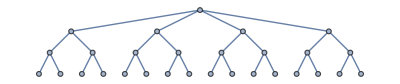

```mathematica
edges=Union[Sort/@Flatten[MapIndexed[Thread[First[#2]<->#]&,A3]]];
g=Graph[Range[Length[A3]],edges]
```

```mathematica
B1={{1},{0}} + 1;
```



```mathematica
edges=Union[Sort/@Flatten[MapIndexed[Thread[First[#2]<->#]&,B1]]];
g=Graph[Range[Length[B1]],edges]
```

```mathematica
B2 = {{1},{0},{1},{1}} + 1
```

{{2},{1},{2},{2}}



```mathematica
edges=Union[Sort/@Flatten[MapIndexed[Thread[First[#2]<->#]&,B2]]];
g=Graph[Range[Length[B2]],edges]
```

```mathematica
B3 ={{1},{0,2,3},{1,4,5},{1,6,7},{2},{2},{3},{3}}+1
```

{{2},{1,3,4},{2,5,6},{2,7,8},{3},{3},{4},{4}}

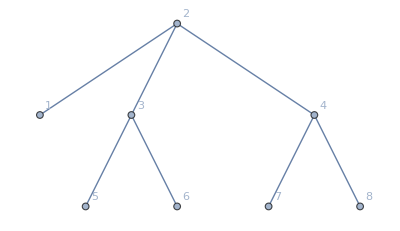

```mathematica
edges=Union[Sort/@Flatten[MapIndexed[Thread[First[#2]<->#]&,B3]]];
g=Graph[Range[Length[B3]],edges, VertexLabels->"Name"]
```

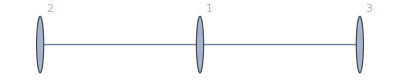

```mathematica
C1 = {{1},{},{0}}+1;
edges=Union[Sort/@Flatten[MapIndexed[Thread[First[#2]<->#]&,C1]]];
g=Graph[Range[Length[C1]],edges, VertexLabels->"Name"]
```

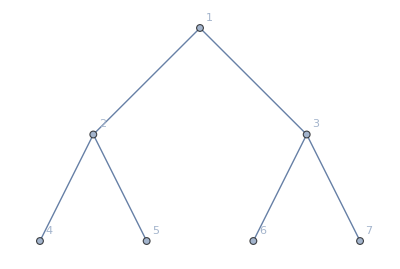

```mathematica
C2 = {{1},{3,4},{0,5,6},{1},{1},{2},{2}}+1;
edges=Union[Sort/@Flatten[MapIndexed[Thread[First[#2]<->#]&,C2]]];
g=Graph[Range[Length[C2]],edges, VertexLabels->"Name"]
```

{{0,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,1,1,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0}}

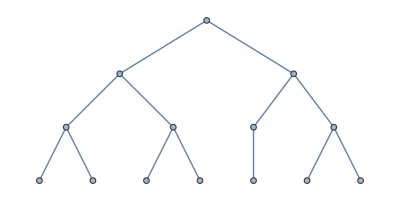

```mathematica
C3 = ({{0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}})
g=AdjacencyGraph[C3]
```